{107.45,213.46,300.,350.38,408.17,449.7,506.9,551.36,603.28,733.24,779.84,825.1,871.22,904.6,943.4,1000.,1200.,1450.,1800.,2019.6}

{11545.5,45565.2,90000.,122766.,166603.,202230.,256948.,303998.,363947.,537641.,608150.,680790.,759024.,818301.,890004.,1.×10^6,1.44×10^6,2.1025×10^6,3.24×10^6,4.07878×10^6}

{14656.7,7323.33,4772.61,3656.67,2753.16,2281.67,1740.,1302.5,944.545,271.25,240.,637.059,836.154,1040.,1212.22,1456.67,2381.3,3323.33,4573.33,5228.1}

{2.14818×10^8,5.36312×10^7,2.27778×10^7,1.33712×10^7,7.57988×10^6,5.206×10^6,3.0276×10^6,1.69651×10^6,892166.,73576.6,57600.,405844.,699153.,1.0816×10^6,1.46948×10^6,2.12188×10^6,5.67061×10^6,1.10445×10^7,2.09154×10^7,2.7333×10^7}

{{11545.5,2.14818×10^8},{45565.2,5.36312×10^7},{90000.,2.27778×10^7},{122766.,1.33712×10^7},{166603.,7.57988×10^6},{202230.,5.206×10^6},{256948.,3.0276×10^6},{303998.,1.69651×10^6},{363947.,892166.},{537641.,73576.6},{608150.,57600.},{680790.,405844.},{759024.,699153.},{818301.,1.0816×10^6},{890004.,1.46948×10^6},{1.×10^6,2.12188×10^6},{1.44×10^6,5.67061×10^6},{2.1025×10^6,1.10445×10^7},{3.24×10^6,2.09154×10^7},{4.07878×10^6,2.7333×10^7}}

FittedModel[-8.789×10^6+(2.59574×10^12)/x+8.70239 x]

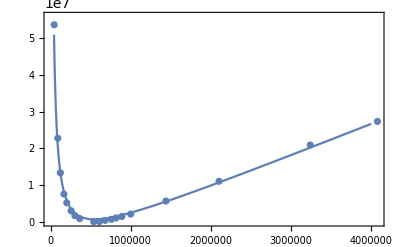
-Graphics-|Z|^2f^2

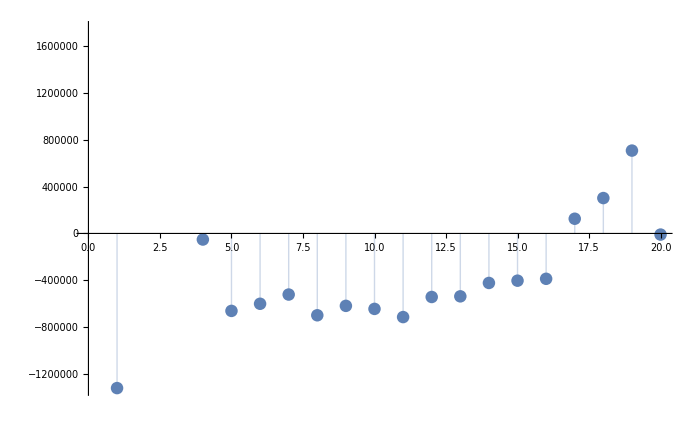

```mathematica
A={107.45,213.46,300.0,350.38,408.17,449.7,506.9,551.36,603.28,733.24,779.84,825.1,871.22,904.6,943.4,1000.0,1200.0,1450.0,1800.0,2019.6}

A = A^2

B={14656.666666666666,7323.333333333333,4772.608695652174,3656.666666666667,2753.157894736842,2281.6666666666665,1740.0,1302.5,944.5454545454546,271.25,240.0,637.0588235294117,836.1538461538461,1040.0,1212.2222222222222,1456.6666666666667,2381.304347826087,3323.333333333333,4573.333333333333,5228.095238095238}

B = B^2

data=Transpose[{A,B}]
nlm=NonlinearModelFit[data,a x+b/x+c,{a,b,c},x]
Labeled[Show[ListPlot[data],Plot[nlm[x],{x,0,4000000}],Frame->True],{"|Z|^2","f^2"},{Left,Bottom},RotateLabel->False]
nlm["FitResiduals"];
ListPlot[%,Filling->Axis]
```

```mathematica
FittedModel[-8.788995357683891*^6+(2.5957385328506616*^12)/x+8.702394391400247 x]
```

FittedModel[-8.789×10^6+(2.59574×10^12)/x+8.70239 x]

```mathematica
Show[%82,ImageSize->Large]
```

```mathematica
Show[%83,AxesLabel->{HoldForm[f^2],RawBoxes[RowBox[{"|","Z",SuperscriptBox["|","2"]}]]},PlotLabel->HoldForm[Schwingkreis Fitfunktion],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%63,ImageSize->Large]
```

```mathematica
Show[%64,AxesLabel->{HoldForm[f^2],RawBoxes[RowBox[{"expression",RowBox[{RowBox[{"(",RowBox[{"paste",RowBox[{"(",RowBox[{"\"|\"",","," ","Z",","," ","\"|\""}],")"}]}],")"}],"^","2"}]}]]},PlotLabel->HoldForm[Fitfunktion Schwingkreis],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%65,ImageSize->Medium]
```

```mathematica
Show[%66,ImageSize->Large]
```

```mathematica
Show[%67,AxesLabel->{HoldForm[TEST],RawBoxes[RowBox[{"expression",RowBox[{RowBox[{"(",RowBox[{"paste",RowBox[{"(",RowBox[{"\"|\"",","," ","Z",","," ","\"|\""}],")"}]}],")"}],"^","2"}]}]]},PlotLabel->None]
```